```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.7,cj->U/5,U->5,t23->x t22,t22->0.3}
```

{Δ→0.7,𝒿→U/5,U→5,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

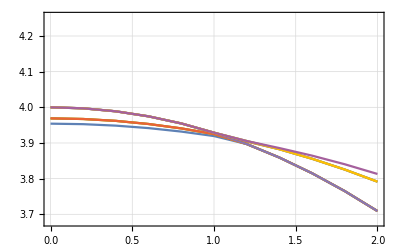

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

-6.58733×10^-17

1

0.0000756567

1

0.000302761

1

0.000681716

1

0.00121318

1

0.00189808

1

0.00273758

1

0.00373305

1

0.00488609

1

0.00619848

1

0.00767216

1

0.00930918

1

5.88247

1

5.86018

1

5.83574

1

5.8092

1

5.78062

1

5.75009

1

5.71775

1

5.68375

1

5.64828

2

2.

2

1.99989

2

1.99954

2

1.99896

2

1.99815

2

1.9971

2

1.9958

2

1.99426

2

1.99246

2

1.99039

2

1.98805

2

5.90263

2

5.88247

2

5.86018

2

5.83574

2

5.8092

2

5.78062

2

5.75009

2

5.71775

2

5.68375

2

5.64828

3

2.

3

1.99989

3

1.99954

3

1.99896

3

1.99815

3

1.9971

3

1.9958

3

1.99426

3

1.99246

3

1.99039

3

1.98805

3

5.90263

3

5.88247

3

5.86018

3

5.83574

3

5.8092

3

5.78062

3

5.75009

3

5.71775

3

5.68375

3

5.64828

4

2.

4

1.99989

4

1.99954

4

1.99896

4

1.99815

4

1.9971

4

1.9958

4

1.99426

4

1.99246

4

1.99039

4

1.98805

4

5.90263

4

5.88247

4

5.86018

4

5.83574

4

5.8092

4

5.78062

4

5.75009

4

5.71775

4

5.68375

4

5.64828

5

6.

5

5.99927

5

5.99709

5

5.99341

5

5.9882

5

5.98139

5

5.97292

5

5.96269

5

5.95063

5

5.93665

5

5.92067

5

5.90263

5

5.88247

5

5.86018

5

5.83574

5

5.8092

5

5.78062

5

5.75009

5

5.71775

5

5.68375

5

5.64828

6

6.

6

5.99927

6

5.99709

6

5.99341

6

5.9882

6

5.98139

6

5.97292

6

5.96269

6

5.95063

6

5.93665

6

5.92067

6

5.90263

6

0.0111117

6

1.97929

6

1.97576

6

1.9719

6

1.9677

6

1.96315

6

1.95825

6

1.95297

6

1.94731

7

6.

7

5.99927

7

5.99709

7

5.99341

7

5.9882

7

5.98139

7

5.97292

7

5.96269

7

5.95063

7

5.93665

7

5.92067

7

1.98543

7

1.98251

7

1.97929

7

1.97576

7

1.9719

7

1.9677

7

1.96315

7

1.95825

7

1.95297

7

1.94731

8

6.

8

5.99927

8

5.99709

8

5.99341

8

5.9882

8

5.98139

8

5.97292

8

5.96269

8

5.95063

8

5.93665

8

5.92067

8

1.98543

8

1.98251

8

1.97929

8

1.97576

8

1.9719

8

1.9677

8

1.96315

8

1.95825

8

1.95297

8

1.94731

9

6.

9

5.99927

9

5.99709

9

5.99341

9

5.9882

9

5.98139

9

5.97292

9

5.96269

9

5.95063

9

5.93665

9

5.92067

9

1.98543

9

1.98251

9

0.0130819

9

0.0152219

9

0.017534

9

0.0200202

9

0.0226823

9

0.0255221

9

0.0285408

9

0.0317395

10

0.75

10

0.749972

10

0.74989

10

0.749752

10

0.749561

10

0.749317

10

0.749021

10

0.748674

10

0.748279

10

0.747836

10

0.747349

10

0.74682

10

0.74625

10

0.745643

10

0.745001

10

0.744327

10

0.743624

10

0.742894

10

0.742141

10

0.741368

10

0.740578

```mathematica
data1//MatrixForm
```

(1 | 0. | -6.58733×10^-17 | 3.95415
1 | 0.1 | 0.0000756567 | 3.95381
1 | 0.2 | 0.000302761 | 3.95277
1 | 0.3 | 0.000681716 | 3.95104
1 | 0.4 | 0.00121318 | 3.94862
1 | 0.5 | 0.00189808 | 3.9455
1 | 0.6 | 0.00273758 | 3.94169
1 | 0.7 | 0.00373305 | 3.93718
1 | 0.8 | 0.00488609 | 3.93196
1 | 0.9 | 0.00619848 | 3.92604
1 | 1. | 0.00767216 | 3.91941
1 | 1.1 | 0.00930918 | 3.91207
1 | 1.2 | 5.88247 | 3.89708
1 | 1.3 | 5.86018 | 3.87888
1 | 1.4 | 5.83574 | 3.85915
1 | 1.5 | 5.8092 | 3.8379
1 | 1.6 | 5.78062 | 3.81512
1 | 1.7 | 5.75009 | 3.79083
1 | 1.8 | 5.71775 | 3.76503
1 | 1.9 | 5.68375 | 3.73775
1 | 2. | 5.64828 | 3.70902
2 | 0. | 2. | 3.96901
2 | 0.1 | 1.99989 | 3.96857
2 | 0.2 | 1.99954 | 3.96725
2 | 0.3 | 1.99896 | 3.96506
2 | 0.4 | 1.99815 | 3.96198
2 | 0.5 | 1.9971 | 3.95803
2 | 0.6 | 1.9958 | 3.95319
2 | 0.7 | 1.99426 | 3.94747
2 | 0.8 | 1.99246 | 3.94087
2 | 0.9 | 1.99039 | 3.93337
2 | 1. | 1.98805 | 3.92498
2 | 1.1 | 5.90263 | 3.91375
2 | 1.2 | 5.88247 | 3.89708
2 | 1.3 | 5.86018 | 3.87888
2 | 1.4 | 5.83574 | 3.85915
2 | 1.5 | 5.8092 | 3.8379
2 | 1.6 | 5.78062 | 3.81512
2 | 1.7 | 5.75009 | 3.79083
2 | 1.8 | 5.71775 | 3.76503
2 | 1.9 | 5.68375 | 3.73775
2 | 2. | 5.64828 | 3.70902
3 | 0. | 2. | 3.96901
3 | 0.1 | 1.99989 | 3.96857
3 | 0.2 | 1.99954 | 3.96725
3 | 0.3 | 1.99896 | 3.96506
3 | 0.4 | 1.99815 | 3.96198
3 | 0.5 | 1.9971 | 3.95803
3 | 0.6 | 1.9958 | 3.95319
3 | 0.7 | 1.99426 | 3.94747
3 | 0.8 | 1.99246 | 3.94087
3 | 0.9 | 1.99039 | 3.93337
3 | 1. | 1.98805 | 3.92498
3 | 1.1 | 5.90263 | 3.91375
3 | 1.2 | 5.88247 | 3.89708
3 | 1.3 | 5.86018 | 3.87888
3 | 1.4 | 5.83574 | 3.85915
3 | 1.5 | 5.8092 | 3.8379
3 | 1.6 | 5.78062 | 3.81512
3 | 1.7 | 5.75009 | 3.79083
3 | 1.8 | 5.71775 | 3.76503
3 | 1.9 | 5.68375 | 3.73775
3 | 2. | 5.64828 | 3.70902
4 | 0. | 2. | 3.96901
4 | 0.1 | 1.99989 | 3.96857
4 | 0.2 | 1.99954 | 3.96725
4 | 0.3 | 1.99896 | 3.96506
4 | 0.4 | 1.99815 | 3.96198
4 | 0.5 | 1.9971 | 3.95803
4 | 0.6 | 1.9958 | 3.95319
4 | 0.7 | 1.99426 | 3.94747
4 | 0.8 | 1.99246 | 3.94087
4 | 0.9 | 1.99039 | 3.93337
4 | 1. | 1.98805 | 3.92498
4 | 1.1 | 5.90263 | 3.91375
4 | 1.2 | 5.88247 | 3.89708
4 | 1.3 | 5.86018 | 3.87888
4 | 1.4 | 5.83574 | 3.85915
4 | 1.5 | 5.8092 | 3.8379
4 | 1.6 | 5.78062 | 3.81512
4 | 1.7 | 5.75009 | 3.79083
4 | 1.8 | 5.71775 | 3.76503
4 | 1.9 | 5.68375 | 3.73775
4 | 2. | 5.64828 | 3.70902
5 | 0. | 6. | 4.
5 | 0.1 | 5.99927 | 3.9993
5 | 0.2 | 5.99709 | 3.9972
5 | 0.3 | 5.99341 | 3.99369
5 | 0.4 | 5.9882 | 3.98877
5 | 0.5 | 5.98139 | 3.98242
5 | 0.6 | 5.97292 | 3.97465
5 | 0.7 | 5.96269 | 3.96542
5 | 0.8 | 5.95063 | 3.95473
5 | 0.9 | 5.93665 | 3.94257
5 | 1. | 5.92067 | 3.92891
5 | 1.1 | 5.90263 | 3.91375
5 | 1.2 | 5.88247 | 3.89708
5 | 1.3 | 5.86018 | 3.87888
5 | 1.4 | 5.83574 | 3.85915
5 | 1.5 | 5.8092 | 3.8379
5 | 1.6 | 5.78062 | 3.81512
5 | 1.7 | 5.75009 | 3.79083
5 | 1.8 | 5.71775 | 3.76503
5 | 1.9 | 5.68375 | 3.73775
5 | 2. | 5.64828 | 3.70902
6 | 0. | 6. | 4.
6 | 0.1 | 5.99927 | 3.9993
6 | 0.2 | 5.99709 | 3.9972
6 | 0.3 | 5.99341 | 3.99369
6 | 0.4 | 5.9882 | 3.98877
6 | 0.5 | 5.98139 | 3.98242
6 | 0.6 | 5.97292 | 3.97465
6 | 0.7 | 5.96269 | 3.96542
6 | 0.8 | 5.95063 | 3.95473
6 | 0.9 | 5.93665 | 3.94257
6 | 1. | 5.92067 | 3.92891
6 | 1.1 | 5.90263 | 3.91375
6 | 1.2 | 0.0111117 | 3.90401
6 | 1.3 | 1.97929 | 3.89445
6 | 1.4 | 1.97576 | 3.88247
6 | 1.5 | 1.9719 | 3.86958
6 | 1.6 | 1.9677 | 3.85579
6 | 1.7 | 1.96315 | 3.84108
6 | 1.8 | 1.95825 | 3.82546
6 | 1.9 | 1.95297 | 3.80893
6 | 2. | 1.94731 | 3.79148
7 | 0. | 6. | 4.
7 | 0.1 | 5.99927 | 3.9993
7 | 0.2 | 5.99709 | 3.9972
7 | 0.3 | 5.99341 | 3.99369
7 | 0.4 | 5.9882 | 3.98877
7 | 0.5 | 5.98139 | 3.98242
7 | 0.6 | 5.97292 | 3.97465
7 | 0.7 | 5.96269 | 3.96542
7 | 0.8 | 5.95063 | 3.95473
7 | 0.9 | 5.93665 | 3.94257
7 | 1. | 5.92067 | 3.92891
7 | 1.1 | 1.98543 | 3.9157
7 | 1.2 | 1.98251 | 3.90553
7 | 1.3 | 1.97929 | 3.89445
7 | 1.4 | 1.97576 | 3.88247
7 | 1.5 | 1.9719 | 3.86958
7 | 1.6 | 1.9677 | 3.85579
7 | 1.7 | 1.96315 | 3.84108
7 | 1.8 | 1.95825 | 3.82546
7 | 1.9 | 1.95297 | 3.80893
7 | 2. | 1.94731 | 3.79148
8 | 0. | 6. | 4.
8 | 0.1 | 5.99927 | 3.9993
8 | 0.2 | 5.99709 | 3.9972
8 | 0.3 | 5.99341 | 3.99369
8 | 0.4 | 5.9882 | 3.98877
8 | 0.5 | 5.98139 | 3.98242
8 | 0.6 | 5.97292 | 3.97465
8 | 0.7 | 5.96269 | 3.96542
8 | 0.8 | 5.95063 | 3.95473
8 | 0.9 | 5.93665 | 3.94257
8 | 1. | 5.92067 | 3.92891
8 | 1.1 | 1.98543 | 3.9157
8 | 1.2 | 1.98251 | 3.90553
8 | 1.3 | 1.97929 | 3.89445
8 | 1.4 | 1.97576 | 3.88247
8 | 1.5 | 1.9719 | 3.86958
8 | 1.6 | 1.9677 | 3.85579
8 | 1.7 | 1.96315 | 3.84108
8 | 1.8 | 1.95825 | 3.82546
8 | 1.9 | 1.95297 | 3.80893
8 | 2. | 1.94731 | 3.79148
9 | 0. | 6. | 4.
9 | 0.1 | 5.99927 | 3.9993
9 | 0.2 | 5.99709 | 3.9972
9 | 0.3 | 5.99341 | 3.99369
9 | 0.4 | 5.9882 | 3.98877
9 | 0.5 | 5.98139 | 3.98242
9 | 0.6 | 5.97292 | 3.97465
9 | 0.7 | 5.96269 | 3.96542
9 | 0.8 | 5.95063 | 3.95473
9 | 0.9 | 5.93665 | 3.94257
9 | 1. | 5.92067 | 3.92891
9 | 1.1 | 1.98543 | 3.9157
9 | 1.2 | 1.98251 | 3.90553
9 | 1.3 | 0.0130819 | 3.89523
9 | 1.4 | 0.0152219 | 3.88572
9 | 1.5 | 0.017534 | 3.87548
9 | 1.6 | 0.0200202 | 3.8645
9 | 1.7 | 0.0226823 | 3.85278
9 | 1.8 | 0.0255221 | 3.84031
9 | 1.9 | 0.0285408 | 3.82709
9 | 2. | 0.0317395 | 3.81311
10 | 0. | 0.75 | 4.65403
10 | 0.1 | 0.749972 | 4.6534
10 | 0.2 | 0.74989 | 4.65149
10 | 0.3 | 0.749752 | 4.64831
10 | 0.4 | 0.749561 | 4.64386
10 | 0.5 | 0.749317 | 4.63814
10 | 0.6 | 0.749021 | 4.63116
10 | 0.7 | 0.748674 | 4.62291
10 | 0.8 | 0.748279 | 4.61341
10 | 0.9 | 0.747836 | 4.60264
10 | 1. | 0.747349 | 4.59063
10 | 1.1 | 0.74682 | 4.57737
10 | 1.2 | 0.74625 | 4.56286
10 | 1.3 | 0.745643 | 4.54712
10 | 1.4 | 0.745001 | 4.53015
10 | 1.5 | 0.744327 | 4.51195
10 | 1.6 | 0.743624 | 4.49254
10 | 1.7 | 0.742894 | 4.47192
10 | 1.8 | 0.742141 | 4.45009
10 | 1.9 | 0.741368 | 4.42707
10 | 2. | 0.740578 | 4.40287)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;12,1;;4]];
tmp02 = data1[[118;;118,1;;4]];
tmp03 = data1[[182;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;32,1;;4]];
tmp02 = data1[[180;;181, 1;;4]];
tmp03 = data1[[119;;126, 1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e1data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.95415 | -6.58733×10^-17
0.1 | 3.95381 | 0.0000756567
0.2 | 3.95277 | 0.000302761
0.3 | 3.95104 | 0.000681716
0.4 | 3.94862 | 0.00121318
0.5 | 3.9455 | 0.00189808
0.6 | 3.94169 | 0.00273758
0.7 | 3.93718 | 0.00373305
0.8 | 3.93196 | 0.00488609
0.9 | 3.92604 | 0.00619848
1. | 3.91941 | 0.00767216
1.1 | 3.91207 | 0.00930918
1.2 | 3.90401 | 0.0111117
1.3 | 3.89523 | 0.0130819
1.4 | 3.88572 | 0.0152219
1.5 | 3.87548 | 0.017534
1.6 | 3.8645 | 0.0200202
1.7 | 3.85278 | 0.0226823
1.8 | 3.84031 | 0.0255221
1.9 | 3.82709 | 0.0285408
2. | 3.81311 | 0.0317395)

(0. | 3.96901 | 2.
0.1 | 3.96857 | 1.99989
0.2 | 3.96725 | 1.99954
0.3 | 3.96506 | 1.99896
0.4 | 3.96198 | 1.99815
0.5 | 3.95803 | 1.9971
0.6 | 3.95319 | 1.9958
0.7 | 3.94747 | 1.99426
0.8 | 3.94087 | 1.99246
0.9 | 3.93337 | 1.99039
1. | 3.92498 | 1.98805
1.1 | 3.9157 | 1.98543
1.2 | 3.90553 | 1.98251
1.3 | 3.89445 | 1.97929
1.4 | 3.88247 | 1.97576
1.5 | 3.86958 | 1.9719
1.6 | 3.85579 | 1.9677
1.7 | 3.84108 | 1.96315
1.8 | 3.82546 | 1.95825
1.9 | 3.80893 | 1.95297
2. | 3.79148 | 1.94731)

(0. | 4. | 6.
0.1 | 3.9993 | 5.99927
0.2 | 3.9972 | 5.99709
0.3 | 3.99369 | 5.99341
0.4 | 3.98877 | 5.9882
0.5 | 3.98242 | 5.98139
0.6 | 3.97465 | 5.97292
0.7 | 3.96542 | 5.96269
0.8 | 3.95473 | 5.95063
0.9 | 3.94257 | 5.93665
1. | 3.92891 | 5.92067
1.1 | 3.91375 | 5.90263
1.2 | 3.89708 | 5.88247
1.3 | 3.87888 | 5.86018
1.4 | 3.85915 | 5.83574
1.5 | 3.8379 | 5.8092
1.6 | 3.81512 | 5.78062
1.7 | 3.79083 | 5.75009
1.8 | 3.76503 | 5.71775
1.9 | 3.73775 | 5.68375
2. | 3.70902 | 5.64828)

```mathematica
|
```

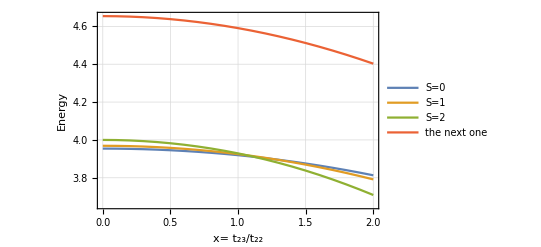

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

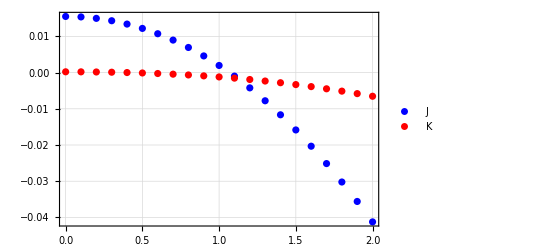

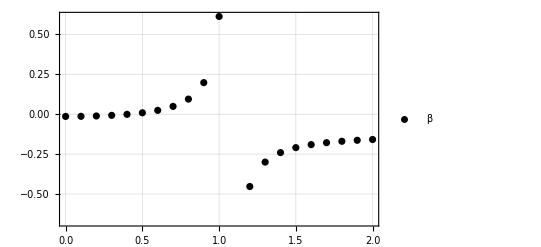

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```